```mathematica
Quiet@Map[SetOptions[#,BaseStyle->{FontSize-> 14,FontFamily->"Times"},LabelStyle->Black,Frame->True,Axes->None,FrameTicksStyle->Black,FrameStyle->Directive[Black,Thickness[0.004]],Method->{"TransparentPolygonMesh"->True}]&,InputForm[Symbol/@Names["System`*Plot"]]];
logticksx=Join[{Log10@#,Switch[#,10^-1,0.1,1,1,10,10,_,Superscript[10,Log10@#]],{.016,0}}&/@(10^Range[-30,33,1]),{Log10@#,"",{.008,0}}&/@Flatten[(10^Range[-30,33,1])*#&/@Range[2,9,1]]];
logticksx2=Join[{Log10@#,"",{.016,0}}&/@(10^Range[-30,33,1]),{Log10@#,"",{.008,0}}&/@Flatten[(10^Range[-30,33,1])*#&/@Range[2,9,1]]];
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->None,RoundingRadius->4,FrameMargins->0,Background->Opacity[0.86,White]]
```

```mathematica
rebin[list_,d_]:=Module[{dold},
dold = list[[2,1]]-list[[1,1]];
{#[[1,1]],dold/d Total[#[[All,2]]]}&/@GatherBy[{Round[#[[1]],d],#[[2]]}&/@list,First]
]
```

```mathematica
klist = {0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.82,0.84,0.86,0.88,0.9,0.92,0.94,0.96,0.98,1.0};
Length@klist
```

18

```mathematica
beta = 5.0;
gamma = 0.0;
```

```mathematica
FkW = ReadList[NotebookDirectory[]<>"FkW_beta_"<>ToString@NumberForm[beta,{3,3}]<>"_gammaperbeta_"<>ToString@NumberForm[gamma,{3,3}]<>".dat",Table[Number,{5}]];
Fk = ReadList[NotebookDirectory[]<>"Fk_beta_"<>ToString@NumberForm[beta,{3,3}]<>"_gammaperbeta_"<>ToString@NumberForm[gamma,{3,3}]<>".dat",Table[Number,{Length@FkW}]];
δk = ReadList[NotebookDirectory[]<>"deltak_beta_"<>ToString@NumberForm[beta,{3,3}]<>"_gammaperbeta_"<>ToString@NumberForm[gamma,{3,3}]<>".dat",Table[Number,{Length@FkW}]];Φk = ReadList[NotebookDirectory[]<>"phik_beta_"<>ToString@NumberForm[beta,{3,3}]<>"_gammaperbeta_"<>ToString@NumberForm[gamma,{3,3}]<>".dat",Table[Number,{Length@FkW}]];
ΦBk = ReadList[NotebookDirectory[]<>"phiBk_beta_"<>ToString@NumberForm[beta,{3,3}]<>"_gammaperbeta_"<>ToString@NumberForm[gamma,{3,3}]<>".dat",Table[Number,{Length@FkW}]];
ktHlists = ReadList[NotebookDirectory[]<>"klist_beta_"<>ToString@NumberForm[beta,{3,3}]<>"_gammaperbeta_"<>ToString@NumberForm[gamma,{3,3}]<>".dat",Table[Number,{3}]];
```

```mathematica
tp = Select[FkW[[All,{1,2}]],#[[2]]<0.3&][[1,1]]
tk = ktHlists[[13,2]]
```

0.87283

1.25926

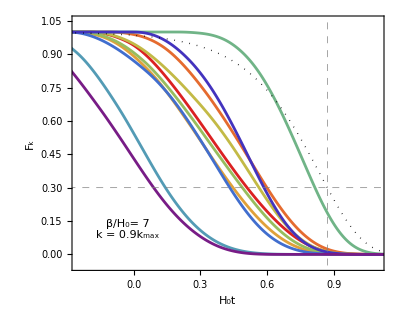
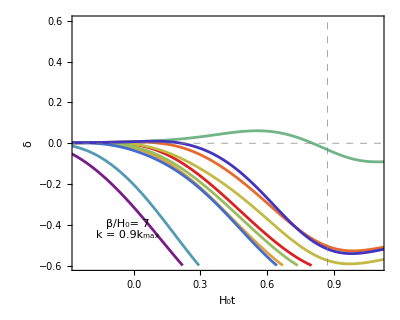
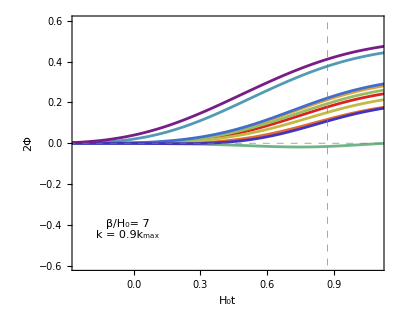

```mathematica
Row@{Show[ListPlot[Transpose@{FkW[[All,1]],Fk[[#]]}&/@Range[1,Length@Fk,1],Joined->True,PlotStyle->Reverse@(ColorData["Rainbow"]/@Subdivide[0,1,9]),PlotRange->{{-0.25,1.1},{-0.05,1.05}}],
ListPlot[FkW[[All,{1,2}]],Joined->True,PlotStyle->Directive[Thick,Black,Dotted]],
Graphics[Style[Text["β/H_0= 7\nk = 0.9k_max",Scaled@{0.18,0.16},TextAlignment->Left],{Black,FontSize-> 14,FontFamily->"Times"}]],
Graphics[Style[Rotate[Text[frame["t = t_p"],Scaled@{0.76,0.8}],90Degree],{Black,FontSize-> 14,FontFamily->"Times"}]],
Graphics[Style[Rotate[Text[frame["t = t_k"],Scaled@{0.92,0.8}],90Degree],{Black,FontSize-> 14,FontFamily->"Times"}]],FrameLabel->{"H_0t","F_k"},ImagePadding->{{52,4},{38,8}},ImageSize->{Automatic,280},AspectRatio->0.8,GridLines->{{tp,tk},{0.3}},GridLinesStyle->Directive[Gray, Dashed]],
Show[ListPlot[Transpose@{FkW[[All,1]],δk[[#]]}&/@Range[1,Length@Fk,1],Joined->True,PlotStyle->Reverse@(ColorData["Rainbow"]/@Subdivide[0,1,9]),PlotRange->{{-0.25,1.1},{-0.6,0.6}},GridLines->{{tp,tk},{0}},GridLinesStyle->Directive[Gray, Dashed]],
Graphics[Style[Rotate[Text[frame["t = t_p"],Scaled@{0.76,0.8}],90Degree],{Black,FontSize-> 14,FontFamily->"Times"}]],
Graphics[Style[Rotate[Text[frame["t = t_k"],Scaled@{0.92,0.8}],90Degree],{Black,FontSize-> 14,FontFamily->"Times"}]],
Graphics[Style[Text["β/H_0= 7\nk = 0.9k_max",Scaled@{0.18,0.16},TextAlignment->Left],{Black,FontSize-> 14,FontFamily->"Times"}]],FrameLabel->{"H_0t","δ"},ImagePadding->{{80,4},{38,8}},ImageSize->{Automatic,280},AspectRatio->0.8],
Show[ListPlot[Transpose@{FkW[[All,1]],2Φk[[#]]}&/@Range[1,Length@Fk,1],Joined->True,PlotStyle->Reverse@(ColorData["Rainbow"]/@Subdivide[0,1,9]),PlotRange->{{-0.25,1.1},{-0.6,0.6}},GridLines->{{tp,tk},{0}},GridLinesStyle->Directive[Gray, Dashed]],
Graphics[Style[Rotate[Text[frame["t = t_p"],Scaled@{0.76,0.8}],90Degree],{Black,FontSize-> 14,FontFamily->"Times"}]],
Graphics[Style[Rotate[Text[frame["t = t_k"],Scaled@{0.92,0.8}],90Degree],{Black,FontSize-> 14,FontFamily->"Times"}]],
Graphics[Style[Text["β/H_0= 7\nk = 0.9k_max",Scaled@{0.18,0.16},TextAlignment->Left],{Black,FontSize-> 14,FontFamily->"Times"}]],FrameLabel->{"H_0t","2Φ"},ImagePadding->{{80,4},{38,8}},ImageSize->{Automatic,280},AspectRatio->0.8]}
```

```mathematica
δbins = ReadList[NotebookDirectory[]<>"deltabinsk_beta_"<>ToString@NumberForm[beta,{3,3}]<>"_gammaperbeta_"<>ToString@NumberForm[gamma,{3,3}]<>".dat",Table[Number,{19}]];
Φbins = ReadList[NotebookDirectory[]<>"phibinsk_beta_"<>ToString@NumberForm[beta,{3,3}]<>"_gammaperbeta_"<>ToString@NumberForm[gamma,{3,3}]<>".dat",Table[Number,{19}]];
ΦBbins = ReadList[NotebookDirectory[]<>"phiBbinsk_beta_"<>ToString@NumberForm[beta,{3,3}]<>"_gammaperbeta_"<>ToString@NumberForm[gamma,{3,3}]<>".dat",Table[Number,{19}]];
```

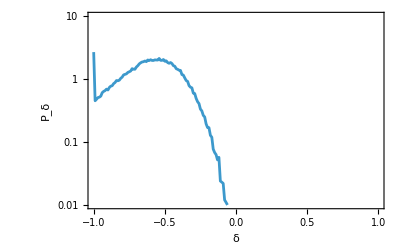

```mathematica
ListLogPlot[{rebin[δbins[[All,{1,13}]],0.01]},PlotRange->{{-1,1},{0.01,10}},Joined->True,FrameLabel->{"δ","P_δ"}]
```